# Movement detection with flicker supression

```mathematica
raw=Import[ToFileName[ParentDirectory[NotebookDirectory[]] <> "/samples/","flicker.mov"], "Data"];
```

```mathematica
nframes=Length[raw]
```

97

```mathematica
Dimensions[raw]
```

{97,480,640,3}

```mathematica
raw[[1,1,1]]
```

{255,255,255}

```mathematica
orig =Map[(#.{0.3,0.59,0.11})&,raw,{3}];
```

```mathematica
scaleFactor = 2;
```

```mathematica
meanKernel=BoxMatrix[scaleFactor]/((2*scaleFactor+1)^2);
MatrixForm[meanKernel]
```

(1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25
1/25 | 1/25 | 1/25 | 1/25 | 1/25)

```mathematica
origc=Map[ListConvolve[meanKernel,#,{-1,-1},0]& ,orig];
```

```mathematica
origdim=Dimensions[orig]
```

{97,480,640}

```mathematica
bwm=Map[Take[#,{1,origdim[[2]],scaleFactor},{1,origdim[[3]],scaleFactor}]&,origc];
```

```mathematica
Dimensions[bwm]
```

{97,240,320}

```mathematica
Manipulate[Image[bwm[[f]],"Byte"] ,{f,1,nframes,1}]
```

```mathematica
linAdjust[trg_,src_] := Fit[Transpose[{Flatten[src], Flatten[trg]}]
,{1,x},x] /. x->src
```

```mathematica
GraphicsRow[{Image[bwm[[13]],"Byte"],Image[linAdjust[bwm[[14]],bwm[[13]]],"Byte"],Image[bwm[[14]],"Byte"]}]
```

-Graphics-

```mathematica
avgFrame[d_] := Total[d]/Length[d]
```

```mathematica
avgFilter[l_,w_]:= 
	Map[avgFrame[l[[Max[1,#-w];;#]]] &, Range[Length[l]]]
```

```mathematica
avgLinFilter[l_,w_]:= 
	Map[avgFrame[
    Map[Function[x,linAdjust[l[[#]],x]] ,
l[[Max[1,#-w];;#]]]
] &, Range[Length[l]]]
```

```mathematica
bwms=avgFilter[bwm,10];
```

```mathematica
Manipulate[ImageAdjust[Image[bwm[[f]]-bwms[[f]], "Byte"]],{f,1,nframes,1}]
```

```mathematica
Mean[Flatten[bwm[[14]]-bwms[[14]]]]
```

5.77839

```mathematica
Mean[Flatten[bwm[[14]]-bwmsl[[14]]]]
```

-1.07399×10^-12

```mathematica
bwmsl=avgLinFilter[bwm,10];
```

```mathematica
Mean[Flatten[bwm[[14]]-bwmsl[[14]]]]
```

-1.07399×10^-12

```mathematica
Manipulate[ImageAdjust[Image[bwm[[f]]-bwmsl[[f]], "Byte"]],{f,1,nframes,1}]
```

```mathematica
errs = Map[RootMeanSquare[Flatten[bwm[[#]]-bwms[[#]]]] / Mean[Flatten[bwm[[#]]]]&, Range[nframes]];
```

```mathematica
errsl = Map[RootMeanSquare[Flatten[bwm[[#]]-bwmsl[[#]]]] / Mean[Flatten[bwm[[#]]]]&, Range[nframes]];
```

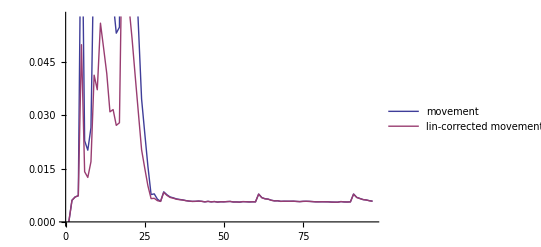

```mathematica
ListLinePlot[{errs,errsl}, PlotLegends ->{"movement","lin-corrected movement"}]
```

```mathematica
lmsmoothPoint[d_] := Module[{data,rdata},
	data = Transpose[{Range[Length[d]],d}];
	rdata =Select[data,NumberQ[N[#[[2]]]]&];
	If[Length[rdata]<2,
		Last[d],
		Fit[rdata,{1,x},x] /. x-> Length[d]
	]
]
```

```mathematica
lmsmooth[l_,w_]:= 
	Map[lmsmoothPoint[l[[Max[1,#-w];;#]]] &, Range[Length[l]]]
```

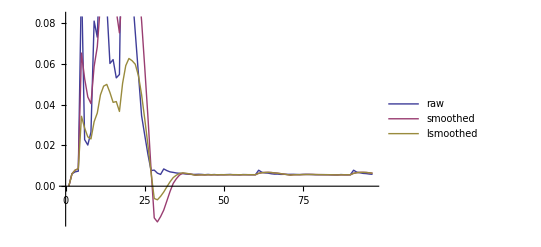

```mathematica
serrs=lmsmooth[errs,10];
serrsl=lmsmooth[errsl,10];
ListLinePlot[{errs,serrs,serrsl},PlotLegends ->{"raw","smoothed","lsmoothed"}]
```

```mathematica
motionThreshold=0.05;
motionFlag=UnitStep[serrs-motionThreshold]
```

{0,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

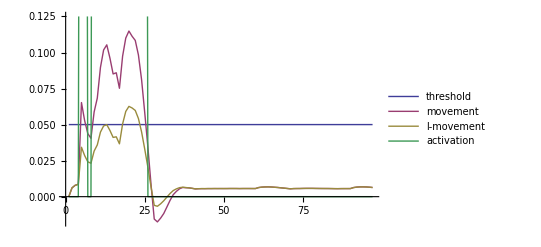

```mathematica
ListLinePlot[{Table[motionThreshold,{nframes}],serrs,serrsl,motionFlag},
PlotLegends ->{"threshold","movement","l-movement","activation"}
]
```